### Parameters

```mathematica
Clear["Global`*"]

chop[x_,a_,b_]:=Which[x>b,b,a≤x≤b,x,x<a,a];  (*Energy store function*)

(* System Parameters *)
T=20; (* Iterations *)
M=3; (* Number of patches *)
c=10; (* Maximum energy *)
xc=3; (* Minimum energy for survival *)
v=Table[0,{i,1,M}]; (* Store the patches survival probabilities on each iteration *)
d=Table[0,{i,1,c}];(* Store the optimal patch index *)

(* Patch Parameters *)
(* Change to foraging time options *)
(* Ftimes: 10 opciones *)

β={0,0.004,0.02}; (* Patch probability of predation, This is not present in logistic growth [here] *)
α={1,1,1}; (* Patch foraging cost ---> Changes, cost for foraging time (proportional). Can be exponential more realistic. 
α = α(ft) = ρ.ft increasing.
*)
λ={0,0.4,0.6};(* Patch probability of finding food ---> Changes, should decrease with population, is constant for all foraging times at a given time, depends only on the current status of the population.
λ = λ(ft, x, p)
must be increasing in ft and decreasing in x.
p = prob of finding food per ftime.
*)
Y={0,3,5}; (* 
Increment in the state variable given that food is found 
	Y = Y(ft) = ⋁.ft 
⋁: velocity of digestion.

Final:
- Use:
- In the logistic growth -> r = r(E) = r.E

- Compare with classical (static)
- Decision (ft per day) plot and Energy plot (E per day).
	- Find some parameters that are meaningful. (Find examples).
*)
x00 = 4;
```

### Routine

```mathematica
f1=Table[If[i≤xc,0,1 ],{i,c}]; (* Final survival proabilities *)
(* At t=T we only care if the forager is alive or dead *)
(* In this case all values x>xc are equally valuable *)

f0=Table[0,{i,c}]; (* Survival probability state *)

fall={}; (*Matrix to store all variable states*)
dall={}; (*Matrix to store all patch selections*)

For[t=T-1,t>0,t--, (* Times loop *)
For[x=xc+1,x≤ c,x++, (* Energy loop *)
For[j=1,j≤M,j++, (* Patches loop *)
(* Evaluate survival probability for each patch *)
v[[j]]=(1-β[[j]])(λ[[j]]f1[[chop[x-α[[j]]+Y[[j]],xc,c]]]+(1-λ[[j]])f1[[chop[x-α[[j]],xc,c]]])

];

(* Get the maximum survival probability value for each energy level x *)
vm=Max[v]; 

(* Store the maximum survival probability value for each energy level x *)
f0[[x]]=SetPrecision[vm,3];

(* Get the patch that maximizes survival, the optimal decision at time t, or each energy level x *)
d[[x]]=Position[v,vm][[1,1]]; 
];

AppendTo[fall,f0]; (* Store the vector with the maximum survival probabilities at time t in the matrix fall *)
AppendTo[dall,d]; (* Store the vector with the optimal patch deicision at time t in the matrix dall *)

(* Update the survivial probabilities *)
f1=f0;
];

(* Maximum survival probability *)
fopt=Transpose[fall[[;;,xc+1;;c]]];
dopt=Transpose[dall[[;;,xc+1;;c]]];

(* Optimal patch selection *)
(* Single trajectory *)

xVector={x00}; (*State variable*)

fopttraj={}; (*Variable state*)
dopttraj={};(*Optimal patch index*)

ftest=Table[If[i≤xc,0,1 ],{i,c}];
t=1;

vals = {};

If[
ftest[[chop[Last[xVector],xc,c]]]==1,

While[t< T,

fopttraj=AppendTo[fopttraj,fopt[[Last[xVector]-xc,-t]] ];
dopttraj=AppendTo[dopttraj,dopt[[Last[xVector]-xc,-t]] ];

xVector=AppendTo[xVector,chop[Last[xVector]-α[[Last[dopttraj]]]+Y[[Last[dopttraj]]],xc,c]];

t=t+1],

0];
```

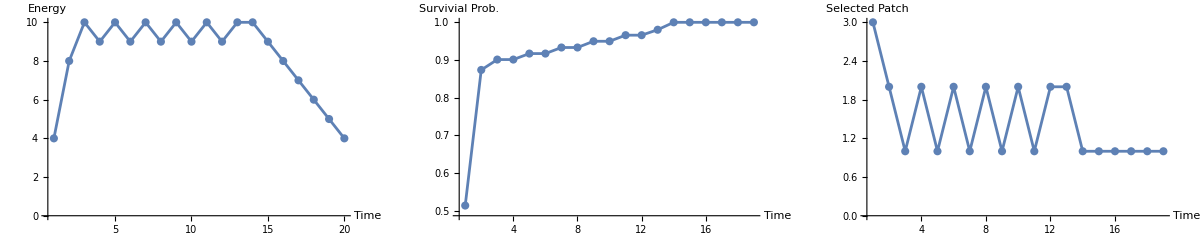

```mathematica
GraphicsRow[{ListLinePlot[xVector,AxesLabel-> {"Time","Energy"},LabelStyle->Directive[Bold,12],ImageSize->300,PlotRange->All,Mesh->All],
ListLinePlot[fopttraj,AxesLabel-> {"Time","Survivial Prob."},LabelStyle->Directive[Bold,12],ImageSize->300,PlotRange->All,Mesh->All],
ListLinePlot[dopttraj,AxesLabel-> {"Time","Selected Patch"},LabelStyle->Directive[Bold,12],ImageSize->300,PlotRange->All,Mesh->All]}]
```

```mathematica
xVector
fopttraj
dopttraj
```

{4,8,10,9,10,9,10,9,10,9,10,9,10,10,9,8,7,6,5,4}

{0.514,0.874,0.901,0.901,0.917,0.917,0.933,0.933,0.95,0.95,0.966,0.966,0.98,1.,1.,1.,1.,1.,1.}

{3,2,1,2,1,2,1,2,1,2,1,2,2,1,1,1,1,1,1}

### Spatial embedding

1= left, 2=up, 3= right, start at point {0,0}

```mathematica
curloc={5,0};
allloc={curloc};

For[i=1,i<T-1,i++,
des=dopttraj[[i]];
Which[
des==1,curloc={curloc[[1]]-1,curloc[[2]]},
des==2,curloc={curloc[[1]],curloc[[2]]+1},
des==3,curloc={curloc[[1]]+1,curloc[[2]]}
];
AppendTo[allloc,curloc]
]
```

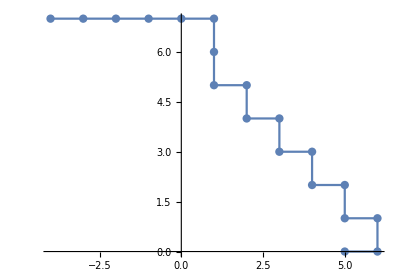

```mathematica
p1=ListLinePlot[allloc,Mesh->All];

env=Table[Table[0,{x,11}],{y,11}];
p2=MatrixPlot[env];
Show[p1,AspectRatio->Automatic]
```

```mathematica
allloc
```

{{5,0},{6,0},{6,1},{5,1},{5,2},{4,2},{4,3},{3,3},{3,4},{2,4},{2,5},{1,5},{1,6},{1,7},{0,7},{-1,7},{-2,7},{-3,7},{-4,7}}

-Graphics-

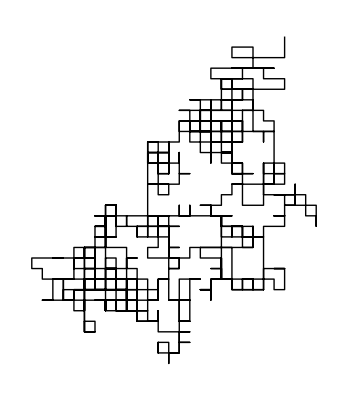

```mathematica
Graphics[Line[Accumulate[RandomChoice[{{-1,0},{1,0},{0,1},{0,-1}},1000]]]]
```